# Signal-2

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

```mathematica
signal=∑_(k=1)^6 Sin[200(2k-1) π t]/((2k-1) π)
```

Sin[200 π t]/π+Sin[600 π t]/(3 π)+Sin[1000 π t]/(5 π)+Sin[1400 π t]/(7 π)+Sin[1800 π t]/(9 π)+Sin[2200 π t]/(11 π)

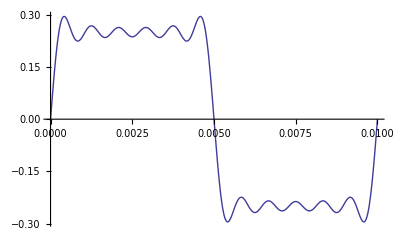

```mathematica
Plot[signal,{t,0,0.01}]
```

```mathematica
play=Play[signal,{t,0,3}]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT

### Get current notebook name without extension

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-4}]
```

Signal-2

### Creat file name with extension

```mathematica
fileName=StringJoin[CurrentNotebookName,".wav"]
```

Signal-2.wav

### Export

```mathematica
Export[fileName,play]
```

Signal-2.wav